{{456.01,4.8}}

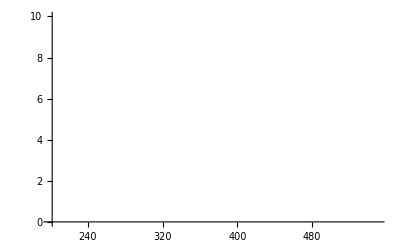

```mathematica
ClearAll["Global`*"]

P=4.3;
R=8.31447;

(*P=2; (*MPa*)
R=8.31447;
ωA=.099;
ωB=.349;
TcA=305.4;
TcB=540.3;
PcA=4.88;
PcB=2.736;*)

ωA=.099;
ωB=.349;
TcA=305.4;
TcB=540.3;
PcA=4.88;
PcB=2.736;

TrA=T/TcA;
TrB=T/TcB;

PsatA=PcA*10^((7/3)*(1+ωA)*(1-1/TrA));
PsatB=PcB*10^((7/3)*(1+ωB)*(1-1/TrB));

PsatAb=PcA*10^((7/3)*(1+ωA)*(1-1/(Tb/TcA)));
PsatBb=PcB*10^((7/3)*(1+ωB)*(1-1/(Tb/TcB)));
PsatAd=PcA*10^((7/3)*(1+ωA)*(1-1/(Td/TcA)));
PsatBd=PcB*10^((7/3)*(1+ωB)*(1-1/(Td/TcB)));

BubbleT=Tb/.Table[FindRoot[P==PsatAb*xAbub+PsatBb*(1-xAbub),{Tb,200,600}],{xAbub,0,1,.01}];
DewT=Td/.Table[FindRoot[P==1/(yAdew/PsatAd+(1-yAdew)/PsatBd),{Td,200,600}],{yAdew,0,1,.01}];

ListLinePlot[{BubbleT,DewT},DataRange->{0,1}];

zA=.3;
zB=1-zA;
i=2;
n=Floor[zA*100+1];

T={BubbleT[[n]],DewT[[n]]};
T=T[[i]];

Tdata=Reap[
Do[
P=P+.1;

KAi=PsatA/P;
KBi=PsatB/P;

T={BubbleT[[n]],DewT[[n]]};
T=T[[i]];

If[i==1,
{yA=KAi*zA,yB=KBi*zB,xA=zA,xB=zB},
{yA=zA,yB=zB,xA=zA/KAi,xB=zB/KBi}];

k=0;
Do[
j=0;
Do[
j++;
PrA=P/PcA;
PrB=P/PcB;
κA=.37464+1.54226*ωA-.26993*ωA^2;
κB=.37464+1.54226*ωB-.26993*ωB^2;
αA=(1+κA*(1-(T/TcA)^.5))^2;
αB=(1+κB*(1-(T/TcB)^.5))^2;
acA=.457235529*R^2*TcA^2/PcA;
acB=.457235529*R^2*TcB^2/PcB;
aA=acA*αA;
aB=acB*αB;
bA=.077796074*R*TcA/PcA;
bB=.077796074*R*TcB/PcB;
A11=aA*P/(R^2*T^2);
A22=aB*P/(R^2*T^2);
B1=bA*P/(R*T);
B2=bB*P/(R*T);
A12=(A11*A22)^.5;
AV=(yA*A11+yB*A12)*yA+(yA*A12+yB*A22)*yB;
BV=yA*B1+yB*B2;
AL=(xA*A11+xB*A12)*xA+(xA*A12+xB*A22)*xB;
BL=xA*B1+xB*B2;
a0=-(AV*BV-BV^2-BV^3);
a1=AV-3*BV^2-2*BV;
a2=-(1-BV);
a0L=-(AL*BL-BL^2-BL^3);
a1L=AL-3*BL^2-2*BL;
a2L=-(1-BL);

p=(3*a1-a2^2)/3;
q=(2*a2^3-9*a2*a1+27*a0)/27;
RrootV=q^2/4+p^3/27;
If[RrootV>0,ponerootV=CubeRoot[-q/2+Sqrt[RrootV]]];
If[RrootV>0,qonerootV=CubeRoot[-q/2-Sqrt[RrootV]]];

pL=(3*a1L-a2L^2)/3;
qL=(2*a2L^3-9*a2L*a1L+27*a0L)/27;
RrootL=qL^2/4+pL^3/27;
If[RrootL>0,ponerootL=CubeRoot[-qL/2+Sqrt[RrootL]]];
If[RrootL>0,qonerootL=CubeRoot[-qL/2-Sqrt[RrootL]]];

If[RrootV<0,m=2*Sqrt[-p/3],m=1];
If[RrootL<0,mL=2*Sqrt[-pL/3],mL=1];
If[RrootV<0,θ=ArcCos[3*q/p/m]/3,θ=0];
If[RrootL<0,θL=ArcCos[3*qL/pL/mL]/3,θL=0];
rootV=m*Cos[θ];
rootL=mL*Cos[θL+2*Pi/3];
If[m==1,ZV=(ponerootV+qonerootV)-a2/3,ZV=rootV-a2/3];
If[mL==1,ZL=(ponerootL+qonerootL)-a2L/3,ZL=rootL-a2L/3];

φV1=Exp[(B1/BV)*(ZV-1)-Log[ZV-BV]-(AV/(BV*Sqrt[8]))*Log[(ZV+(1+Sqrt[2])*BV)/(ZV+(1-Sqrt[2])*BV)]*(2*(yA*A11+yB*A12)/AV-B1/BV)];
φV2=Exp[(B2/BV)*(ZV-1)-Log[ZV-BV]-(AV/(BV*Sqrt[8]))*Log[(ZV+(1+Sqrt[2])*BV)/(ZV+(1-Sqrt[2])*BV)]*(2*(yA*A12+yB*A22)/AV-B2/BV)];
φL1=Exp[(B1/BL)*(ZL-1)-Log[ZL-BL]-(AL/(BL*Sqrt[8]))*Log[(ZL+(1+Sqrt[2])*BL)/(ZL+(1-Sqrt[2])*BL)]*(2*(xA*A11+xB*A12)/AL-B1/BL)];
φL2=Exp[(B2/BL)*(ZL-1)-Log[ZL-BL]-(AL/(BL*Sqrt[8]))*Log[(ZL+(1+Sqrt[2])*BL)/(ZL+(1-Sqrt[2])*BL)]*(2*(xA*A12+xB*A22)/AL-B2/BL)];

KA=φL1/φV1;
KB=φL2/φV2;

If[i==1,
{yA=KA*zA,yB=KB*zB,xA=zA,xB=zB},
{yA=zA,yB=zB,xA=zA/KA,xB=zB/KB}];
ysum=yA+yB;
xsum=xA+xB;
check[j]=ysum;
If[check[j]-check[j-1]<.01,Break[]];
yA=yA/ysum;
yB=yB/ysum;
xA=xA/xsum;
xA=xA/xsum;
,100000];

k++;
If[i==1,
If[ysum>1,T=T-.001,T=T+.001],
If[xsum>1,T=T+.001,T=T-.001]];
check2[k]=T;
If[check2[k-2]-check2[k]==0,Break[]];
,100000];

If[i==1,Tbub=T,Tdew=T];
Sow[{Tdew,P}];
,1]];

Tdata=Flatten[Tdata[[2]],1]
aqw=Thread[{Tdata[[All,1]],Tdata[[All,2]]}];
ListLinePlot[aqw,PlotRange->{{200,550},{0,10}}]
```